# Half Space, Albedo Problem, Isotropic Scattering

## Exponential Random Flight

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2016 Eugene d’Eon 
www.eugenedeon.com

## Path Setup

Put a file at ~/.hitchhikerpath with the path to your hitchhiker repo so that these worksheets can find the MC data from the C++ simulations for verification

```mathematica
SetDirectory[Import["~/.hitchhikerpath"]]
```

## Notation

α - single-scattering albedo
Σt - extinction coefficient
z - depth in medium (positive inside the scattering half space)
u = cos θ - direction cosine

## Caseology

### Caseology quantities

```mathematica
CaseN0[c_,v0_]:=1/2 c v0^3 (c/(v0^2-1)-1/v0^2)
```

```mathematica
Casev0[c_?NumericQ]:=FindRoot[c v ArcTanh[1/v]-1==0,{v,1.00000000001,10^10},Method->"Brent"][[1]][[2]]
```

```mathematica
CaseN[c_,v_]:=v (Caseλ[v,c]^2+((π c v)/2)^2)
```

```mathematica
Caseλ[v_,c_]:=1-c v ArcTanh[v]
```

```mathematica
Caseψ0[u_,v0_,c_,z_]:=c/2 v0/(v0-Sign[z]u)
```

## H-function

### H-function (Stibbs-Weir)

```mathematica
halfspaceAlbedoProblemIsotropic`H[α_,u_]:=Exp[-u/Pi NIntegrate[Log[1-α t Cot[t]]/(Cos[t]^2+u^2 Sin[t]^2),{t,0,Pi/2}]]
```

```mathematica
halfspaceAlbedoProblemIsotropic`Hmoment[α_,j_]:=NIntegrate[H[α,u] u^j,{u,0,1}]
```

### Approximate H-function

```mathematica
Clear[n,y];
halfspaceAlbedoProblemIsotropic`H2[α_,u_]:=(1-(1-y)u(n+(1-n/2-n u)Log[(1+u)/u]))^-1/.n->(1-y)/(1+y)/.y->(1-α)^(1/2)
```

```mathematica
halfspaceAlbedoProblemIsotropic`HmomentApprox[α_,j_]:=1/(j+1)2/(1+y)(1+j/(2(j+2))(1-y)/(1+y))/.y->√(1-α)
```

## Albedo

### Exact Solution

```mathematica
halfspaceAlbedoProblemIsotropic`albedoexact[α_,ui_]:=1-√(1-α)halfspaceAlbedoProblemIsotropic`H[α,ui]
```

```mathematica
halfspaceAlbedoProblemIsotropic`albedoexact[α_]:=NIntegrate[2 u halfspaceAlbedoProblemIsotropic`albedoexact[α,u],{u,0,1}]
```

### Single-scattered Albedo (Exact Solution)

```mathematica
halfspaceAlbedoProblemIsotropic`albedoSingleScatterExact[α_,ui_]:=1/2 α (1+ui Log[ui/(1+ui)])
```

```mathematica
halfspaceAlbedoProblemIsotropic`albedoSingleScatterExact[α_]:=2/3 (α-α Log[2])
```

### Double-scattered Albedo (Exact Solution)

```mathematica
halfspaceAlbedoProblemIsotropic`albedoDoubleScatterExact[α_,ui_]:=-1/8 α^2 (-1+Log[ⅇ^(2 ui^2 (Log[1-ui] Log[ui]-PolyLog[2,ui/(-1+ui)]))]+2 ui (ui Log[1+1/ui]^2+Log[(4 ui)/(1+ui)]-ui Log[1-ui] Log[1+ui])+2 ui^2 (PolyLog[2,-1/ui]+PolyLog[2,(1+ui)/(-1+ui)]))
```

```mathematica
halfspaceAlbedoProblemIsotropic`albedoDoubleScatterExact[α_]:=1/24 c^2 (4+π^2-16 Log[2])
```

### Approximate General Albedos

Classical Diffusion

```mathematica
halfspaceAlbedoProblemIsotropic`albedoClassicalDiffusion[c_,ui_]:=c/((1+2/3(3(1-c))^(1/2))(1+(3(1-c))^(1/2) ui))
```

Rigorous Diffusion

```mathematica
halfspaceAlbedoProblemIsotropic`albedoRigorousDiffusion[c_,ui_]:=c/((1+(2(1-c))/#)(1+# ui))&[1/Casev0[c]]
```

Grosjean Modified Diffusion 1

```mathematica
halfspaceAlbedoProblemIsotropic`albedoGrosjeanDiffusion1[c_,ui_]:=c/2(1-ui Log[(1+ui)/ui])(1-(c(13-5c))/(13-5c+16/3(2-c)K))+(c^2(13-5c))/((1+K ui)(13-5c+16/3(2-c)K))-5/4(K c^2(2-c)(1-2 ui+2 ui^2 Log[(1+ui)/ui]))/(13-5c+16/3(2-c)K)/.K->((3(1-c))/(2-c))^(1/2)
```

Grosjean Modified Diffusion 2

```mathematica
halfspaceAlbedoProblemIsotropic`albedoGrosjeanDiffusion2[c_,ui_]:=c/2(1-ui Log[(1+ui)/ui])(1-c/(1+(2(2-c)K)/3))+c^2/((1+K ui)(1+(2(2-c)K)/3))/.K->((3(1-c))/(2-c))^(1/2)
```

### Approximate Normal Incidence Albedos

[Pomraning 1965]

```mathematica
halfspaceAlbedoProblemIsotropic`albedoNormalPomraning[α_]:=2/((1+#)Log[1-#^2])(Log[1+#]-#)&[1/Casev0[α]]
```

[Prahl 2002]

```mathematica
halfspaceAlbedoProblemIsotropic`albedoNormalPrahl[α_]:= ((1-#)(1-0.128#))/(1+1.83 #)&[√(1-α)]
```

### Approximate WhiteSky Albedos

Integral of H2

```mathematica
halfspaceAlbedoProblemIsotropic`albedoH2[α_]:=NIntegrate[2 u (1-√(1-α)halfspaceAlbedoProblemIsotropic`H2[α,u]),{u,0,1}]
```

[Pomraning 1965]

```mathematica
halfspaceAlbedoProblemIsotropic`albedoWhiteskyPomraning[α_]:=-4/(#^2 Log[1-#^2])(Log[1+#]-#)^2&[1/Casev0[α]]
```

[van de Hulst 1980]

```mathematica
halfspaceAlbedoProblemIsotropic`albedoWhiteskyVanDeHulst[α_]:=((1-#)(1-0.139#))/(1+1.17 #)&[√(1-α)]
```

## BRDF

### Exact Solution

```mathematica
halfspaceAlbedoProblemIsotropic`BRDF[α_,ui_,uo_]:=(α halfspaceAlbedoProblemIsotropic`H2[α,ui]halfspaceAlbedoProblemIsotropic`H2[α,uo])/(4Pi(ui+uo))
```

```mathematica
halfspaceAlbedoProblemIsotropic`BRDFsinglescatter[α_,ui_,uo_]:=α 1/(4 Pi)1/(ui+uo)
```

```mathematica
halfspaceAlbedoProblemIsotropic`BRDFdoublescatter[α_,ui_,uo_]:=α^2/(4 Pi)(ui ArcCoth[1+2 ui]+uo ArcCoth[1+2 uo])/(ui+uo)
```

## Load MC Data

### Delta Incidence

```mathematica
halfspaceAlbedoProblemIsotropic`deltafs=FileNames["code/3D_medium/halfspace/albedoProblem/data/albedoproblem_delta*.txt"];
```

```mathematica
halfspaceAlbedoProblemIsotropic`indexdelta[x_]:=Module[{data,α,Σt,ui},
data=Import[x,"Table"];
Σt=data[[2,5]];
α=data[[2,3]];
ui=data[[1,-1]];
{α,Σt,ui,data}];
halfspaceAlbedoProblemIsotropic`simulationsdelta=halfspaceAlbedoProblemIsotropic`indexdelta/@halfspaceAlbedoProblemIsotropic`deltafs;
halfspaceAlbedoProblemIsotropic`alphas=Union[#[[1]]&/@halfspaceAlbedoProblemIsotropic`simulationsdelta]
```

{0.01,0.1,0.3,0.5,0.7,0.8,0.9,0.95,0.99,0.999}

```mathematica
halfspaceAlbedoProblemIsotropic`muts=Union[#[[2]]&/@halfspaceAlbedoProblemIsotropic`simulationsdelta]
```

{1}

```mathematica
halfspaceAlbedoProblemIsotropic`uis=Union[#[[3]]&/@halfspaceAlbedoProblemIsotropic`simulationsdelta]
```

{0.1,0.25,0.5,1}

### WhiteSky Illumination

```mathematica
halfspaceAlbedoProblemIsotropic`whiteskyfs=FileNames["code/3D_medium/halfspace/albedoProblem/data/albedoproblem_whitesky*.txt"];
```

```mathematica
halfspaceAlbedoProblemIsotropic`indexwhitesky[x_]:=Module[{data,α,Σt},
data=Import[x,"Table"];
Σt=data[[2,5]];
α=data[[2,3]];
{α,Σt,data}];
halfspaceAlbedoProblemIsotropic`simulationswhitesky=halfspaceAlbedoProblemIsotropic`indexwhitesky/@halfspaceAlbedoProblemIsotropic`whiteskyfs;
```

### Util

```mathematica
halfspaceAlbedoProblemIsotropic`plotpoints[data_,du_]:=Table[{du i - 0.5 du,data[[i]]},{i,1,Length[data]}];
```

## Albedo Benchmarks

### Normal Incidence

```mathematica
MCMLBenchmarkData={{0.9990009990009991,0.912484},{0.09090909090909091,0.0147879},{0.16666666666666666,0.0286725},{0.3333333333333333,0.0653595},{0.5,0.11524},{0.6666666666666666,0.189042},{0.9090909090909091,0.432273},{0.9950248756218907,0.816965},{0.8333333333333334,0.319804},{0.998003992015968,0.879038},{0.9995002498750625,0.937142},{0.9998000399920016,0.959626},{0.9999000099990001,0.971259},{0.9523809523809523,0.543346},{0.9803921568627451,0.673321},{0.9900990099009901,0.75327}};
```

```mathematica
halfspaceAlbedoProblemIsotropic`normalRs={#[[1]],#[[4]][[3,3]]}&/@Select[halfspaceAlbedoProblemIsotropic`simulationsdelta,#[[3]]==1&]
```

{{0.01,0.0015482},{0.1,0.0164138},{0.3,0.0572445},{0.5,0.115279},{0.7,0.208883},{0.8,0.28562},{0.95,0.535438},{0.999,0.913071},{0.99,0.753413},{0.9,0.414801}}

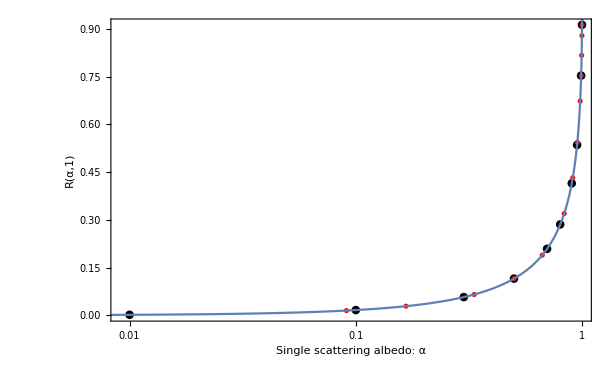

```mathematica
Quiet[Show[
Show[
ListLogLinearPlot[halfspaceAlbedoProblemIsotropic`normalRs,PlotStyle->{PointSize[0.01],Black}],
ListLogLinearPlot[MCMLBenchmarkData,PlotStyle->{PointSize[0.006],Red}],
LogLinearPlot[Quiet[halfspaceAlbedoProblemIsotropic`albedoexact[c,1]],{c,0.001,.9999},PlotRange->All]
],Frame->True,FrameLabel->{{R[α,1],},{"Single scattering albedo: α","Total Reflectance/Albedo R(α): isotropically-scattering half space, normal incidence (u_i=1), indexed matched boundary"}}
]]
```

### Albedo - Delta Illumination - General incidence

```mathematica
Manipulate[
Module[{Rs},
Rs={#[[1]],#[[4]][[3,3]]}&/@Select[halfspaceAlbedoProblemIsotropic`simulationsdelta,#[[3]]==ui&];
Quiet[Show[
Show[
ListLogLinearPlot[Rs,PlotStyle->{PointSize[0.01],Black}],
LogLinearPlot[Quiet[halfspaceAlbedoProblemIsotropic`albedoexact[c,ui]],{c,0.001,.9999},PlotRange->All]
],Frame->True,FrameLabel->{{R[α,ui],},{"Single scattering albedo: α","Total Reflectance/Albedo R(α,u_i): isotropically-scattering half space\nincidence (u_i="<>ToString[ui]<>"), indexed-matched boundary"}}
]]
]
,{ui,halfspaceAlbedoProblemIsotropic`uis}]
```

### Single & Double-Scattered Albedo - Delta Illumination - General incidence

```mathematica
Manipulate[
Module[{RsSingle,RsDouble},
RsSingle={#[[1]],#[[4]][[5,2]]}&/@Select[halfspaceAlbedoProblemIsotropic`simulationsdelta,#[[3]]==ui&];
RsDouble={#[[1]],#[[4]][[5,3]]}&/@Select[halfspaceAlbedoProblemIsotropic`simulationsdelta,#[[3]]==ui&];
Quiet[Show[
Show[
ListLogLinearPlot[RsSingle,PlotStyle->{PointSize[0.01],Black}],
ListLogLinearPlot[RsDouble,PlotStyle->{PointSize[0.01],Black}],
LogLinearPlot[Quiet[halfspaceAlbedoProblemIsotropic`albedoSingleScatterExact[c,ui]],{c,0.001,.9999},PlotRange->All,PlotStyle->Dashed],
LogLinearPlot[Quiet[halfspaceAlbedoProblemIsotropic`albedoDoubleScatterExact[c,ui]],{c,0.001,.9999},PlotRange->All]
],Frame->True,FrameLabel->{{Subscript[R, n][α,ui],},{"Single scattering albedo: α","Single (Dashed) and Double-Scattered Reflectance/Albedo R_n(α,u_i): \nisotropically-scattering half space\nincidence (u_i="<>ToString[ui]<>"), indexed-matched boundary"}}
]]
]
,{ui,halfspaceAlbedoProblemIsotropic`uis}]
```

### Approximate General Albedos

```mathematica
Manipulate[
Module[{Rs},
Rs={#[[1]],#[[4]][[3,3]]}&/@Select[halfspaceAlbedoProblemIsotropic`simulationsdelta,#[[3]]==ui&];
GraphicsRow[{Quiet[Show[
Show[
ListPlot[Rs,PlotStyle->{PointSize[0.01],Black}],
Plot[halfspaceAlbedoProblemIsotropic`albedoClassicalDiffusion[c,ui],{c,0.001,.9999},
PlotRange->All,PlotStyle->Dashed],
Plot[halfspaceAlbedoProblemIsotropic`albedoRigorousDiffusion[c,ui],{c,0.001,.9999},
PlotRange->All,PlotStyle->Red]
],Frame->True,FrameLabel->{{R[α,ui],},{"Single scattering albedo: α",
"Total Reflectance/Albedo R(α,u_i): isotropically-scattering half space\nincidence (u_i="<>ToString[ui]<>"), indexed-matched boundary\nMC(dots), Classical Diffusion (dashed), Rigorous Diffusion (thin)"}},
ImageSize->500
]],
Quiet[Show[
Show[
Plot[halfspaceAlbedoProblemIsotropic`albedoexact[c,ui]-halfspaceAlbedoProblemIsotropic`albedoClassicalDiffusion[c,ui],{c,0.001,.9999},
PlotRange->All,PlotStyle->Dashed],
Plot[halfspaceAlbedoProblemIsotropic`albedoexact[c,ui]-halfspaceAlbedoProblemIsotropic`albedoRigorousDiffusion[c,ui],{c,0.001,.9999},
PlotRange->All,PlotStyle->Red],
Plot[halfspaceAlbedoProblemIsotropic`albedoexact[c,ui]-halfspaceAlbedoProblemIsotropic`albedoGrosjeanDiffusion1[c,ui],{c,0.001,.9999},
PlotRange->All,PlotStyle->DotDashed]
],Frame->True,FrameLabel->{{"R_exact - R_approx",},{"Single scattering albedo: α","Total Reflectance/Albedo R(α,u_i): isotropically-scattering half space\nincidence (u_i="<>ToString[ui]<>"), indexed-matched boundary\nClassical Diffusion (dashed), Rigorous Diffusion (thin), Grosjean1 (DotDashed)"}}
]]
}]
]
,{ui,halfspaceAlbedoProblemIsotropic`uis}]
```

### Normal incidence - Approximate Albedos

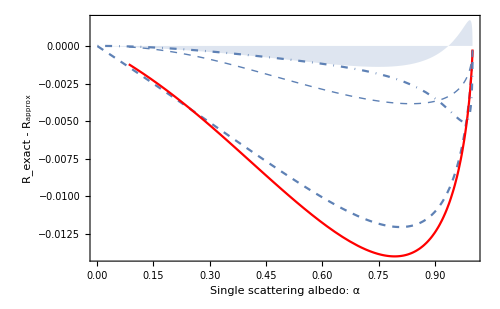

```mathematica
Quiet[Show[
Show[
Plot[halfspaceAlbedoProblemIsotropic`albedoexact[c,1]-halfspaceAlbedoProblemIsotropic`albedoClassicalDiffusion[c,1],{c,0.001,.9999},
PlotRange->All,PlotStyle->Dashed],
Plot[halfspaceAlbedoProblemIsotropic`albedoexact[c,1]-halfspaceAlbedoProblemIsotropic`albedoRigorousDiffusion[c,1],{c,0.001,.9999},
PlotRange->All,PlotStyle->Red],
Plot[halfspaceAlbedoProblemIsotropic`albedoexact[c,1]-halfspaceAlbedoProblemIsotropic`albedoGrosjeanDiffusion1[c,1],{c,0.001,.9999},
PlotRange->All,PlotStyle->DotDashed],
Plot[halfspaceAlbedoProblemIsotropic`albedoexact[c,1]-halfspaceAlbedoProblemIsotropic`albedoNormalPomraning[c],{c,0.001,.9999},
PlotRange->All,PlotStyle->{Thick,Dashed}],
Plot[halfspaceAlbedoProblemIsotropic`albedoexact[c,1]-halfspaceAlbedoProblemIsotropic`albedoNormalPrahl[c],{c,0.001,.9999},
PlotRange->All,PlotStyle->Opacity[0],Filling->Axis]
],Frame->True,ImageSize->500,
FrameLabel->{{"R_exact - R_approx",},{"Single scattering albedo: α","Total Reflectance/Albedo R(α,1): isotropically-scattering half space\nNormal incidence (u_i=1), indexed-matched boundary\nClassical Diffusion (dashed), Rigorous Diffusion (thin), Grosjean1 (DotDashed)\nPomraning (Thick-Dashed), Prahl (Filled)"}}
]]
```

### Albedo - WhiteSky Illumination - Integral using H2 approximation

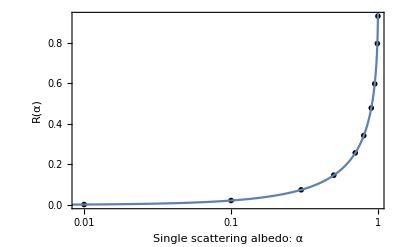

```mathematica
Module[{Rs},
Rs={#[[1]],#[[3]][[3,3]]}&/@halfspaceAlbedoProblemIsotropic`simulationswhitesky;
Quiet[Show[
Show[
ListLogLinearPlot[Rs,PlotStyle->{PointSize[0.01],Black}],
LogLinearPlot[Quiet[halfspaceAlbedoProblemIsotropic`albedoH2[c]],{c,0.001,.9999},PlotRange->All]
],Frame->True,FrameLabel->{{R[α],},{"Single scattering albedo: α","Total Reflectance/Albedo R(α): isotropically-scattering half space\nwhite-sky illumination, indexed-matched boundary"}}
]]
]
```

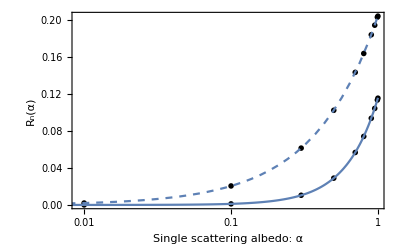

```mathematica
Module[{RsSingle,RsDouble},
RsSingle={#[[1]],#[[3]][[5,2]]}&/@halfspaceAlbedoProblemIsotropic`simulationswhitesky;
RsDouble={#[[1]],#[[3]][[5,3]]}&/@halfspaceAlbedoProblemIsotropic`simulationswhitesky;
Quiet[Show[
Show[
ListLogLinearPlot[RsSingle,PlotStyle->{PointSize[0.01],Black}],
ListLogLinearPlot[RsDouble,PlotStyle->{PointSize[0.01],Black}],
LogLinearPlot[Quiet[halfspaceAlbedoProblemIsotropic`albedoSingleScatterExact[c]],{c,0.001,.9999},PlotRange->All,PlotStyle->Dashed],
LogLinearPlot[Quiet[halfspaceAlbedoProblemIsotropic`albedoDoubleScatterExact[c]],{c,0.001,.9999},PlotRange->All]
],Frame->True,FrameLabel->{{Subscript[R, n][α],},{"Single scattering albedo: α","Single (Dashed) and Double-Scattered Reflectance/Albedo R_n(α): \nIsotropically-Scattering Half Space\nWhite-Sky Illumination, indexed-matched boundary"}}
]
]
]
```

### Approximate White-sky Albedos

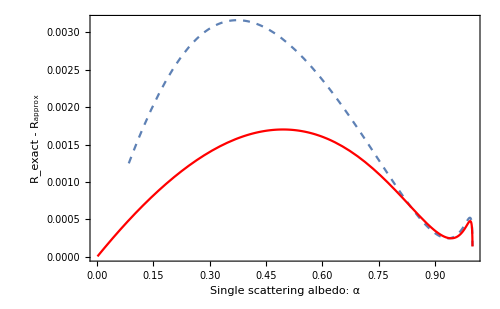

```mathematica
Quiet[Show[
Show[
Plot[halfspaceAlbedoProblemIsotropic`albedoH2[c]-halfspaceAlbedoProblemIsotropic`albedoWhiteskyPomraning[c],{c,0.001,.9999},
PlotRange->All,PlotStyle->Dashed],
Plot[halfspaceAlbedoProblemIsotropic`albedoH2[c]-halfspaceAlbedoProblemIsotropic`albedoWhiteskyVanDeHulst[c],{c,0.001,.9999},
PlotRange->All,PlotStyle->Red]
],Frame->True,ImageSize->500,
FrameLabel->{{"R_exact - R_approx",},{"Single scattering albedo: α","Total Reflectance/Albedo R(α): isotropically-scattering half space\nWhite-sky illumination, indexed-matched boundary\nPomraning (dashed), VanDeHulst (thin)"}}
]]
```

## BRDF Benchmarks

```mathematica
Manipulate[
Module[{emerging,imdata,sim,du,emergingS,emergingD,stride},
sim=SelectFirst[halfspaceAlbedoProblemIsotropic`simulationsdelta,#[[3]]==ui&&#[[1]]==α&&#[[2]]==1&];
imdata=sim[[4]];
du=imdata[[2,7]];
stride=3;
emerging=halfspaceAlbedoProblemIsotropic`plotpoints[imdata[[7]],du][[1;;-1;;stride]];
emergingS=halfspaceAlbedoProblemIsotropic`plotpoints[imdata[[9]],du][[1;;-1;;stride]];
emergingD=halfspaceAlbedoProblemIsotropic`plotpoints[imdata[[11]],du][[1;;-1;;stride]];
Show[
Show[
Plot[2 Pi u halfspaceAlbedoProblemIsotropic`BRDF[α,ui,u],{u,0,1},PlotRange->All],
Plot[2 Pi u halfspaceAlbedoProblemIsotropic`BRDFsinglescatter[α,ui,u],{u,0,1},PlotStyle->Dashed],
Plot[2 Pi u halfspaceAlbedoProblemIsotropic`BRDFdoublescatter[α,ui,u],{u,0,1},PlotStyle->Thick],
ListPlot[emerging,PlotStyle->{PointSize[0.004],Black}],
ListPlot[emergingS,PlotStyle->{PointSize[0.004],Black}],
ListPlot[emergingD,PlotStyle->{PointSize[0.004],Black}]
],Frame->True,ImageSize->500,FrameLabel->{{2 π Subscript[u, o] Subscript[f, r][Subscript[u, i],Subscript[u, o]],},{Subscript[u, o],"Emerging Distribution f_r(u_i,u_o): isotropically-scattering half space\nincidence (u_i="<>ToString[ui]<>"), indexed-matched boundary\nTotal (thin), Single-Scatter (dashed), Double-scatter (thick)"}}
]
]
,
{{α,0.8},halfspaceAlbedoProblemIsotropic`alphas},
{{ui,0.25},halfspaceAlbedoProblemIsotropic`uis}
]
```